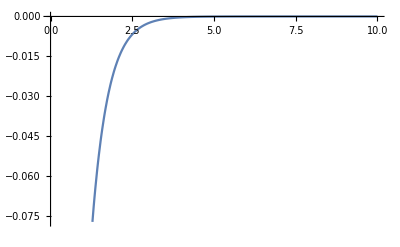

```mathematica
(* Simulating Matrix Differential Eqns*)
ClearAll["Global`*"];
tEnd=10;
X0=({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
A[t_] := ({{-t, 0, 0, 0}, {0, -t, 0, 0}, {0, 0, -t, 0}, {0, 0, 0, -t}});
Af = ({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
Q = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Bf = {0,0,0,0};
sol=x/. NDSolve[{x'[t]==Q  + Afᵀ.x[t] + x[t].Af,x[0]==X0},x,{t,0,tEnd}];
i = 4;j = 4;
Plot[sol[[1]][t][[i]][[j]],{t,0,tEnd}]
```

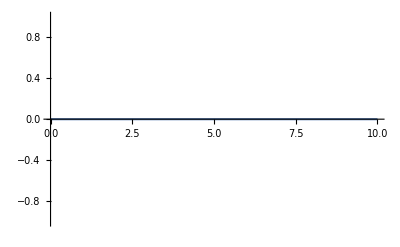

```mathematica
ClearAll["Global`*"];
tEnd=10;
Q = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Af = ({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Bf = {0,0,0,0};

sol2=S/. NDSolve[{S'[t]==Q + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]],S[0]==S0},S,{t,0,tEnd}];
i = 4;j = 4;
Plot[sol2[[1]][t][[i]][[j]],{t,0,tEnd}]
```

```mathematica
ClearAll["Global`*"];
Bf = {0,1,0,0};
S[t_] := ({{t, 0, 0, 0}, {0, t, 0, 0}, {0, 0, t, 0}, {0, 0, 0, t}});
expr[t_] := Outer[Times,S[t].Bf,Bfᵀ.S[t]] - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]];
```

```mathematica
MatrixForm[expr[2]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ClearAll["Global`*"];
n=10;τ=5;τ1=τ*1.25;A=0.2;
ICs={0,0,π,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
```

```mathematica
CalculateGainsIntegrate[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,tCurrent_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState];
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[t], xdot -> xdot1a[t], θ ->θ1a[t], θdot -> θdot1a[t], u -> u1a[t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ - tCurrent}];
S = sol2[[1]][τ - tCurrent];
K = (Bfᵀ.S)/. {x-> x1a[τ - tCurrent], xdot -> xdot1a[τ - tCurrent], θ ->θ1a[τ - tCurrent], θdot -> θdot1a[τ - tCurrent], u -> u1a[τ - tCurrent]}
]
```

```mathematica
ClearAll["Global`*"];
n=10;τ=5;τ1=τ*1.25;A=0.2;
ICs={0.1,0,0,0};




testFBLQR[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{K1,K2,K3,K4,eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,ufb,u,θs,θdots,xs,xdots,us,κ1,κ2,κ3,κ4,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

ufb[t_]:= Module[{K},
K = CalculateGainsIntegrate[x1a,xdot1a,θ1a,θdot1a,u1a,τ,t];
Piecewise[{{K[[3]]*(θff[t]-θ[t])+K[[4]] *(θdotff[t]-θdot[t])+K[[1]]*(xff[t]-x[t])+K[[2]] * (xdotff[t]-xdot[t]),0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])]
];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:= Module[{K},
K = CalculateGainsIntegrate[x1a,xdot1a,θ1a,θdot1a,u1a,τ,t];
uff[t] + Piecewise[{{K[[3]]*(θff[t]-θs[t])+K[[4]] *(θdotff[t]-θdots[t])+K[[1]]*(xff[t]-xs[t])+K[[2]] * (xdotff[t]-xdots[t]),0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])]
];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

```mathematica
n=10;τ=5;τ1=τ*1.25;A=0.2;
ICs={0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];  
testFBLQR[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t$189003 == 0..

Set::shape: Lists {xs$189003,xdots$189003,θs$189003,θdots$189003} and NDSolveValue[{{x$189003'[t$189003]==xdot$189003[t$189003],xdot$189003'[t$189003]==(Piecewise[{«1»},0]+Piecewise[{«1»},Plus[«4»]]+0.2 Cos[«1»] Sin[«1»]+0.2 Sin[«1»] Power[«2»])/(1+Times[«2»]),θ$189003'[t$189003]==θdot$189003[t$189003],θdot$189003'[t$189003]==(-Sin[«1»]-Cos[«1»] Plus[«3»])/(1+Times[«2»])},{x$189003[0]==0,xdot$189003[0]==0,θ$189003[0]==0,θdot$189003[0]==0}},{x$189003,xdot$189003,θ$189003,θdot$189003},{t$189003,0,6.25},Method→{DiscontinuityProcessing→None}] are not the same shape.

NIntegrate::inumr: The integrand ((Piecewise[{{Piecewise[{{«2»}},0], 0≤t$189003≤5}, {0, True}}])+(Piecewise[{{cartPendulum`Private`xdotff$189000 Plus[«2»]+cartPendulum`Private`xff$189000 Plus[«2»]+cartPendulum`Private`θdotff$189000 Plus[«2»]+cartPendulum`Private`θff$189000 Plus[«2»], 0≤t$189003≤5}, {-0.65 (Piecewise[{«1»},0]-xdots$189003[«1»])-0.1 (Piecewise[{«1»},0]-xs$189003[«1»])+3 (Piecewise[{«1»},0]-θdots$189003[«1»])+3 (Piecewise[{«1»},π]-θs$189003[«1»]), True}}]))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{xs$189003,xdots$189003,θs$189003,θdots$189003,us$189003,NIntegrate[us$189003[t$189003]^2,{t$189003,0,5}]}